# Drift - time file

```mathematica
SetDirectory["/home/goluckyryan/Desktop"]
Directory[]
Folder="./mwdc1_dt_sa_old_Gen";
```

/home/goluckyryan/Desktop

/home/goluckyryan/Desktop

```mathematica
RenameFile[Folder<>"/dt_x1.data",Folder<>"/dt_x1.dat"];
RenameFile[Folder<>"/dt_x2.data",Folder<>"/dt_x2.dat"];
RenameFile[Folder<>"/dt_u1.data",Folder<>"/dt_u1.dat"];
RenameFile[Folder<>"/dt_u2.data",Folder<>"/dt_u2.dat"];
RenameFile[Folder<>"/dt_v1.data",Folder<>"/dt_v1.dat"];
RenameFile[Folder<>"/dt_v2.data",Folder<>"/dt_v2.dat"];
```

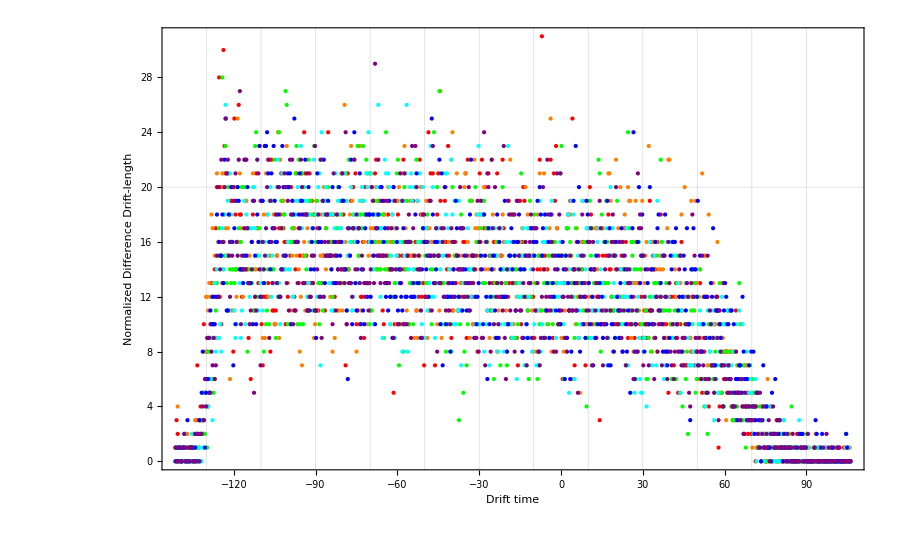

```mathematica
dtx1=Import[Folder<>"/dt_x1.dat"];
dtx2=Import[Folder<>"/dt_x2.dat"];
dtu1=Import[Folder<>"/dt_u1.dat"];
dtu2=Import[Folder<>"/dt_u2.dat"];
dtv1=Import[Folder<>"/dt_v1.dat"];
dtv2=Import[Folder<>"/dt_v2.dat"];
ListPlot[{dtx1,dtx2,dtu1,dtu2,dtv1,dtv2},PlotStyle->{Red,Orange,Green,Cyan,Blue,Purple}
,GridLines->{Table[-130+20 i,{i,0,11}],Table[20 i,{i,1,10}]},
Frame->True,FrameLabel->{"Drift time","Normalized Difference Drift-length"},ImageSize->900]
```

```mathematica
CDTConver[data_]:=Module[{sumAll},
sumAll=Sum[data[[i,2]],{i,1,Length[data]}];
Table[
{data[[i,1]],Sum[data[[j,2]],{j,1,i}]/sumAll 10//N}
,{i,1,Length[data]}]
];
```

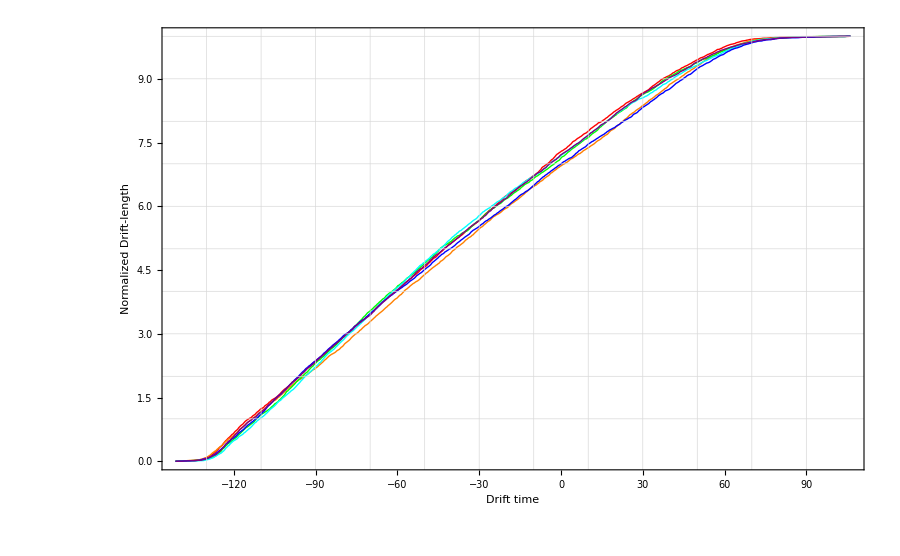

```mathematica
Cdtx1=CDTConver[dtx1];
Cdtx2=CDTConver[dtx2];
Cdtu1=CDTConver[dtu1];
Cdtu2=CDTConver[dtu2];
Cdtv1=CDTConver[dtv1];
Cdtv2=CDTConver[dtv2];
ListPlot[{Cdtx1,Cdtx2,Cdtu1,Cdtu2,Cdtv1,Cdtv2},Joined->True,
PlotStyle->{Red,Orange,Green,Cyan,Blue,Purple},
GridLines->{Table[-130+20 i,{i,0,11}],Table[i,{i,1,10}]},
Frame->True,FrameLabel->{"Drift time","Normalized Drift-length"},ImageSize->900]
```

## From dT to generate DTcL

```mathematica
SetDirectory["/home/goluckyryan/Desktop"]
folderhalf="./mwdc2_dt_sa_valid";
```

/home/goluckyryan/Desktop

```mathematica
binSize[int_,end_,binNum_]:=(end-int)/binNum//N
binList[int_,end_,binNum_,center_]:=If[center,Table[int+(i+1/2) binSize[int,end,binNum],{i,0,binNum-1}],Table[int+i binSize[int,end,binNum],{i,0,binNum-1}]]

Solve[binSize[-141.6,106.4,x]==0.4,x]
dtList=binList[-141.6,106.4,620,True];
Length[dtList]
```

{{x→620.}}

620

```mathematica
dtx1=Flatten[Import[folderhalf<>"/dt_x1.dat"]];
dtx2=Flatten[Import[folderhalf<>"/dt_x2.dat"]];
dtu1=Flatten[Import[folderhalf<>"/dt_u1.dat"]];
dtu2=Flatten[Import[folderhalf<>"/dt_u2.dat"]];
dtv1=Flatten[Import[folderhalf<>"/dt_v1.dat"]];
dtv2=Flatten[Import[folderhalf<>"/dt_v2.dat"]];
```

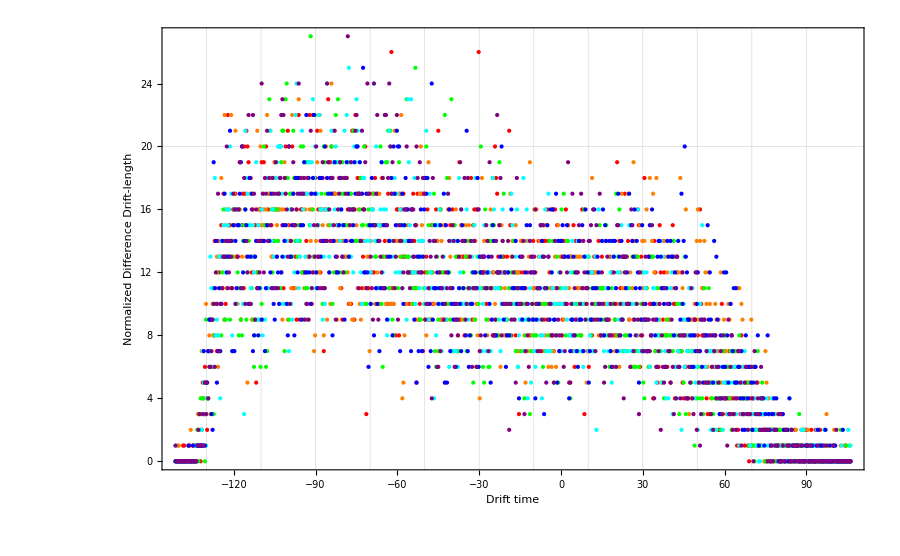

```mathematica
DTcLx1=Table[{dtList[[i]],dtx1[[i]]},{i,1,620}];
DTcLx2=Table[{dtList[[i]],dtx2[[i]]},{i,1,620}];
DTcLu1=Table[{dtList[[i]],dtu1[[i]]},{i,1,620}];
DTcLu2=Table[{dtList[[i]],dtu2[[i]]},{i,1,620}];
DTcLv1=Table[{dtList[[i]],dtv1[[i]]},{i,1,620}];
DTcLv2=Table[{dtList[[i]],dtv2[[i]]},{i,1,620}];
ListPlot[{DTcLx1,DTcLx2,DTcLu1,DTcLu2,DTcLv1,DTcLv2},PlotStyle->{Red,Orange,Green,Cyan,Blue,Purple}
,GridLines->{Table[-130+20 i,{i,0,11}],Table[20 i,{i,1,10}]},
Frame->True,FrameLabel->{"Drift time","Normalized Difference Drift-length"},ImageSize->900]
```

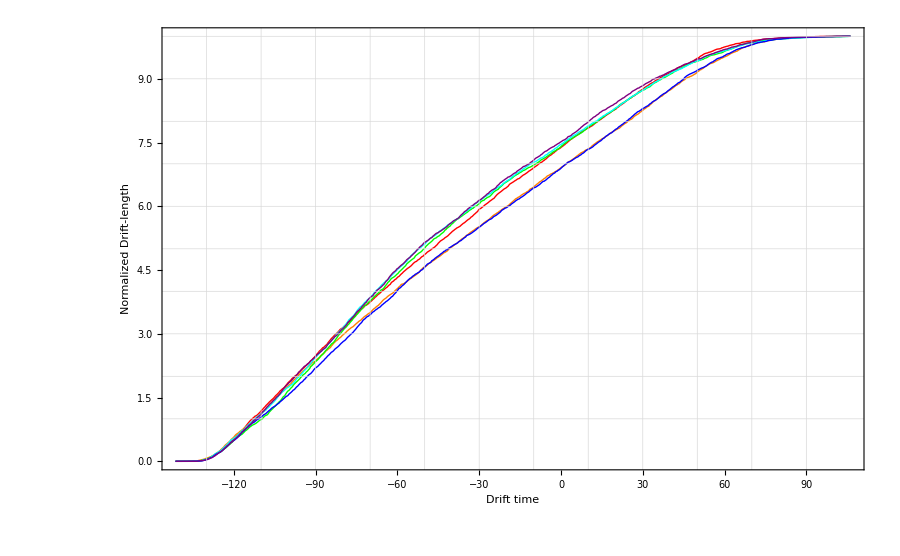

```mathematica
TcLx1=CDTConver[DTcLx1];
TcLx2=CDTConver[DTcLx2];
TcLu1=CDTConver[DTcLu1];
TcLu2=CDTConver[DTcLu2];
TcLv1=CDTConver[DTcLv1];
TcLv2=CDTConver[DTcLv2];
ListPlot[{TcLx1,TcLx2,TcLu1,TcLu2,TcLv1,TcLv2},Joined->True,
PlotStyle->{Red,Orange,Green,Cyan,Blue,Purple},
GridLines->{Table[-130+20 i,{i,0,11}],Table[i,{i,1,10}]},
Frame->True,FrameLabel->{"Drift time","Normalized Drift-length"},ImageSize->900]
```

```mathematica
exportFolder=folderhalf<>"_Gen";
CreateDirectory[exportFolder];
```

```mathematica
(* export format *)
eDTcLx1=Table[{ToString[NumberForm[DTcLx1[[i,1]],{4,4}]],ToString[NumberForm[DTcLx1[[i,2]],{4,4}]]},{i,1,620}];
eDTcLx2=Table[{ToString[NumberForm[DTcLx2[[i,1]],{4,4}]],ToString[NumberForm[DTcLx2[[i,2]],{4,4}]]},{i,1,620}];
eDTcLu1=Table[{ToString[NumberForm[DTcLu1[[i,1]],{4,4}]],ToString[NumberForm[DTcLu1[[i,2]],{4,4}]]},{i,1,620}];
eDTcLu2=Table[{ToString[NumberForm[DTcLu2[[i,1]],{4,4}]],ToString[NumberForm[DTcLu2[[i,2]],{4,4}]]},{i,1,620}];
eDTcLv1=Table[{ToString[NumberForm[DTcLv1[[i,1]],{4,4}]],ToString[NumberForm[DTcLv1[[i,2]],{4,4}]]},{i,1,620}];
eDTcLv2=Table[{ToString[NumberForm[DTcLv2[[i,1]],{4,4}]],ToString[NumberForm[DTcLv2[[i,2]],{4,4}]]},{i,1,620}];
```

```mathematica
Export[exportFolder<>"/dt_x1.dat",eDTcLx1];
Export[exportFolder<>"/dt_x2.dat",eDTcLx2];
Export[exportFolder<>"/dt_u1.dat",eDTcLu1];
Export[exportFolder<>"/dt_u2.dat",eDTcLu2];
Export[exportFolder<>"/dt_v1.dat",eDTcLv1];
Export[exportFolder<>"/dt_v2.dat",eDTcLv2];
```

```mathematica
RenameFile[exportFolder<>"/dt_x1.dat",exportFolder<>"/dt_x1.data"];
RenameFile[exportFolder<>"/dt_x2.dat",exportFolder<>"/dt_x2.data"];
RenameFile[exportFolder<>"/dt_u1.dat",exportFolder<>"/dt_u1.data"];
RenameFile[exportFolder<>"/dt_u2.dat",exportFolder<>"/dt_u2.data"];
RenameFile[exportFolder<>"/dt_v1.dat",exportFolder<>"/dt_v1.data"];
RenameFile[exportFolder<>"/dt_v2.dat",exportFolder<>"/dt_v2.data"];
```

## Find Fit

```mathematica
Data={
{-130,0},
{-100.2, 1.68873},
{-59.8,4.05978},
{-39.8, 5.17994},
{-30.2,5.59692},
{20.2,8.20387},
{36.2,8.90103}};
```

```mathematica
K=NonlinearModelFit[Data,a x^2+b x +c,{a,b,c},x];
K["ANOVATable"]
```

| DF | SS | MS
Model | 3 | 224.012 | 74.6705
Error | 4 | 0.0111895 | 0.00279739
Uncorrected Total | 7 | 224.023 | 
Corrected Total | 6 | 62.452 |

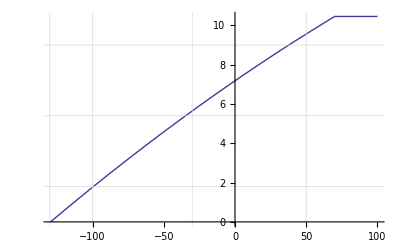

```mathematica
Drift[x_]:=If[x≥ -130 && x ≤ 70,K[x],
If[x<-130,0,K[70]]]
Plot[Drift[x],{x,-130,100},GridLines->{{-130,-100,-30,50},{1.8,5.4,9}},PlotRange->{0,All}]
```

```mathematica
DiscrtDrift[f_,range_,binwidth_]:=Table[{i,Composition[f][i]},{i,range[[1]],range[[2]],binwidth}]
```

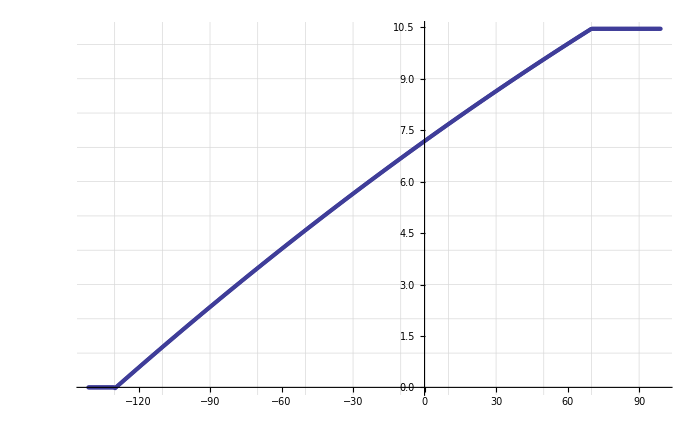

```mathematica
CDT2=DiscrtDrift[Drift,{-141,99},0.4];
ListPlot[CDT2,GridLines->{Table[-130+20 i,{i,0,11}],Table[i,{i,1,10}]},ImageSize->700]
```

```mathematica
CDT2[[-75,2]]
CDT3=Table[{CDT2[[i,1]],CDT2[[i,2]]/CDT2[[-1,2]]},{i,1,Length[CDT2]}];
```

10.4308

```mathematica
ExportFile[cdt_]:=Table[{Floor[10cdt[[i,1]]]/10//N,If[i==1,cdt[[i,2]],cdt[[i,2]]-cdt[[i-1,2]]]},{i,1,Length[cdt]}]
```

4147.39

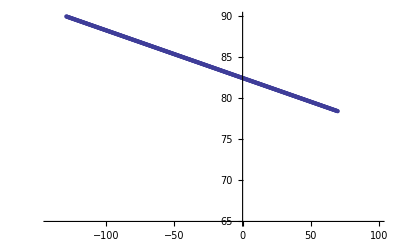

```mathematica
DT2=ExportFile[CDT2];
α=41949/Sum[DT2[[i,2]],{i,1,Length[DT2]}]
DT2a=Table[{DT2[[i,1]],DT2[[i,2]]α},{i,1,Length[DT2]}];
ListPlot[DT2a]
```

```mathematica
DT2a[[33]]
```

{-128.2,89.8185}

```mathematica
NumberForm[DT2a,{4,4}];
```

```mathematica
Export["dt_x1.dat",DT2a,"Data"]
```

dt_x1.dat